```mathematica
m=1
```

1

```mathematica
ω=1
```

1

```mathematica
ℏ=1
```

1

```mathematica
ξ[x_]:=Sqrt[(m ω)/ℏ] x
```

```mathematica
K[E_]:=(2 E)/(ℏ ω)
```

```mathematica
solucion[Evalor_]:=NDSolve[{ψ''[ξ]==(ξ^2-K[Evalor]) ψ[ξ],ψ[0]==1,ψ'[0]==0},ψ,{ξ,0,5}]
```

```mathematica
graficarFuncionDeOnda[Evalor_]:=Module[{sol,ψSol},sol=solucion[Evalor];
ψSol=ψ/. First[sol];
Plot[ψSol[ξ],{ξ,0,5},PlotRange->{-1.5,1.5},(*Ajusta según necesidad*)AxesLabel->{"ξ","ψ(ξ)"},PlotLabel->StringForm["E = `` ℏω",Evalor],ImageSize->Medium]]
```

```mathematica
Manipulate[graficarFuncionDeOnda[k],{k,0.4,0.6,0.001},(*Rango de E cerca de 0.5 ℏω*)ControlPlacement->Top]
```

```mathematica
ξmax=10
```

10

```mathematica
k1=5
```

5

```mathematica
sol1=NDSolve[{ψ''[ξ]==(ξ^2-k1) ψ[ξ],ψ[0]==0,ψ'[0]==1},ψ,{ξ,0,ξmax},Method->"StiffnessSwitching"]
```

{{ψ→InterpolatingFunction[…]}}

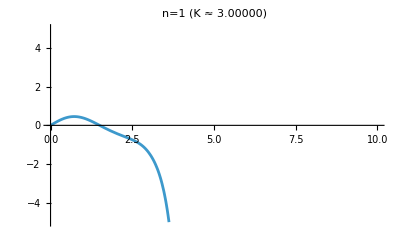

```mathematica
Plot[Evaluate[ψ[ξ]/. sol1],{ξ,0,ξmax},PlotRange->{-5,5},PlotLabel->"n=1 (K ≈ 3.00000)"]
```

```mathematica
k2=5.0
```

5.

```mathematica
sol2=NDSolve[{ψ''[ξ]==(ξ^2-k2) ψ[ξ],ψ[0]==1,ψ'[0]==0},ψ,{ξ,0,ξmax}]
```

{{ψ→InterpolatingFunction[…]}}

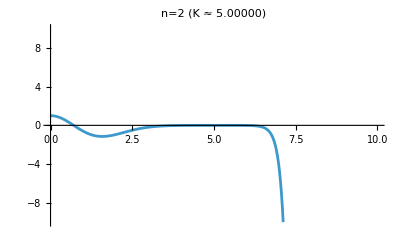

```mathematica
Plot[Evaluate[ψ[ξ]/. sol2],{ξ,0,ξmax},PlotRange->{-10,10},PlotLabel->"n=2 (K ≈ 5.00000)"]
```

```mathematica
k3=7.0
```

7.

```mathematica
sol3=NDSolve[{ψ''[ξ]==(ξ^2-k3) ψ[ξ],ψ[0]==0,ψ'[0]==1},ψ,{ξ,0,ξmax},Method->"StiffnessSwitching"]
```

{{ψ→InterpolatingFunction[…]}}

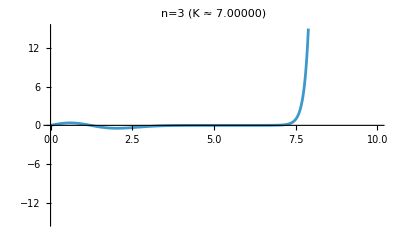

```mathematica
Plot[Evaluate[ψ[ξ]/. sol3],{ξ,0,ξmax},PlotRange->{-15,15},PlotLabel->"n=3 (K ≈ 7.00000)"]
```

```mathematica
ℏ=1;m=1;L=1;
```

```mathematica
EncontrarEnergiaParaPozo[n_]:=Module[{Einicio,Epaso,tolerancia,Eprueba,k,sol,ψ,x,condicion,Eoptima},Einicio=(n^2 π^2 ℏ^2)/(2 m L^2);
Epaso=0.0001;
tolerancia=0.00001;
Eoptima=Einicio;
condicion=False;
While[!condicion,k=Sqrt[2 m Eoptima]/ℏ;
sol=NDSolve[{ψ''[x]+k^2 ψ[x]==0,ψ[0]==0,ψ'[0]==1},ψ,{x,0,L}];
ψSol=ψ/. First[sol];
If[Abs[ψSol[L]]<tolerancia,condicion=True,If[ψSol[L]>0,Eoptima-=Epaso,Eoptima+=Epaso]];
If[Abs[Eoptima-Einicio]>2,Print["Error: No hay convergencia para n = ",n];
Break[];];];
Eoptima]
```

```mathematica
resultados=Table[{n,EncontrarEnergiaParaPozo[n]},{n,1,4}];

Grid[Prepend[resultados,{"Estado (n)","Energía (E_n)"}],Frame->All,Alignment->Center,Background->{None,{LightBlue,None}}]
```

Estado (n) | Energía (E_n)
1 | π^2/2
2 | 2 π^2
3 | (9 π^2)/2
4 | 8 π^2